```mathematica
Experiments with the Double Pendulum

(*
==Double Pendulum==
In physics and mathematics,in the area of dynamical systems,a double pendulum is a pendulum with another pendulum attached to its end,and is a simple physical system that exhibits rich dynamic behavior with a strong sensitivity to initial conditions.[1] The motion of a double pendulum is governed by a set of coupled ordinary differential equations.For certain energies its motion is chaotic.
-https://en.wikipedia.org/wiki/Double_pendulum
-https://www.wolfram.com/mathematica/new-in-9/advanced-hybrid-and-differential-algebraic-equations/double-pendulum.html
*)
```

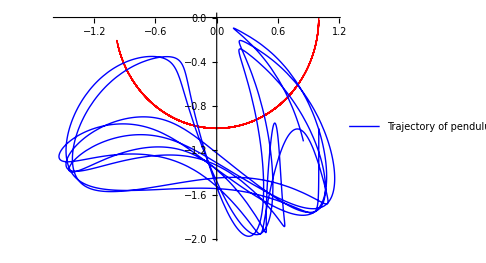

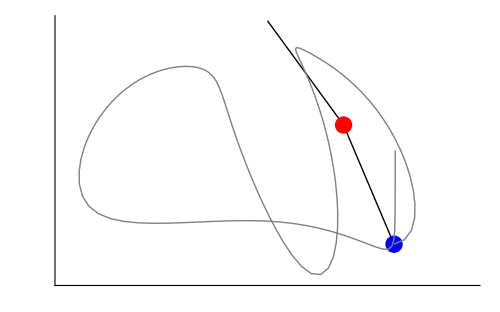

```mathematica
deqns={
Subscript[m,1] x1''[t]==(λ1[t]/Subscript[l,1]) x1[t]-(λ2[t]/Subscript[l,2]) (x2[t]-x1[t]),
Subscript[m,1] y1''[t]==(λ1[t]/Subscript[l,1]) y1[t]-(λ2[t]/Subscript[l,2]) (y2[t]-y1[t])-Subscript[m,1] g,
Subscript[m,2] x2''[t]==(λ2[t]/Subscript[l,2]) (x2[t]-x1[t]),
Subscript[m,2] y2''[t]==(λ2[t]/Subscript[l,2]) (y2[t]-y1[t])-Subscript[m,2] g};

aeqns={x1[t]^2+y1[t]^2==Subscript[l,1]^2,(x2[t]-x1[t])^2+(y2[t]-y1[t])^2==Subscript[l,2]^2};

ics={x1[0]==1,y1[0]==0,x1'[0]==0,y1'[0]==0,x2[0]==1,y2[0]==-1,x2'[0]==0,y2'[0]==0};

params={g->9.81,Subscript[m,1]->1,Subscript[m,2]->1,Subscript[l,1]->1,Subscript[l,2]->1};

soldp=First[NDSolve[{deqns,aeqns,ics}/.params,{x1,y1,x2,y2,λ1,λ2},{t,0,15},Method->{"IndexReduction"->{Automatic,"IndexGoal"->0}}]];

ParametricPlot[Evaluate[{{x1[t],y1[t]},{x2[t],y2[t]}}/.soldp],{t,0,15},PlotStyle->{Red,Blue},ImageSize->Medium,PlotLegends->{"Trajectory of pendulum 1","Trajectory of pendulum 2"}]

Animate[Graphics[{{PointSize[.025],{Red,Point[{x1[t],y1[t]}]},{Blue,Point[{x2[t],y2[t]}]},Line[{{0,0},{x1[t],y1[t]},{x2[t],y2[t]}}]}/.soldp,{Gray,Line[Map[Function[Evaluate[{x2[#],y2[#]}/.soldp]],Range[0,t,0.025]]]}},PlotRange->{{-2,2},{-2,0}},Axes->True,Ticks->False,ImageSize->500],{t,0,20,.025},SaveDefinitions->True]

With[{t=3.7},Graphics[{{Thick,Line[{{0,0},{x1[t],y1[t]},{x2[t],y2[t]}}],PointSize[.025],{Red,Point[{x1[t],y1[t]}]},{Blue,Point[{x2[t],y2[t]}]},}/.soldp,{Gray,Line[Map[Function[Evaluate[{x2[#],y2[#]}/.soldp]],Range[0,t,0.025]]]}},PlotRange->{{-1.6,1.6},{-2,0}},Axes->True,Ticks->False,ImageSize->500]]
```